## Contour Plot - ^135Pr

## Calculating the contour plot of the energy function for a triaxial rotor, using the 2-axis and 3-axis quantization for the moments of inertia.

## Inertial functions

```mathematica
Afct[spin_,oddspin_,a1_,a2_,th_]:=a2(1-(oddspin*Sin[th])/spin)-a1;
ufct[spin_,oddspin_,a1_,a2_,a3_,th_]:=(a3-a1)/Afct[spin,oddspin,a1,a2,th];
v0fct[spin_,oddspin_,a1_,a2_,th_]:=-(a1*oddspin*Cos[th])/Afct[spin,oddspin,a1,a2,th];
vfct[spin_,oddspin_,a1_,a2_,th_]:=v0fct[spin,oddspin,a1,a2,th]/spin;
```

# 2-axis quantization (MOI-2 is the largest)

### Constants

```mathematica
SPIN=19/2;
j=N[11/2];
THETA=N[70*π/180];
I1=10;I2=40;I3=20;
A1=1/(2I1);A2=1/(2I2);A3=1/(2I3);
u[spin_]:=N[ufct[spin,j,A1,A2,A3,THETA]];
v0[spin_]:=N[v0fct[spin,j,A1,A2,THETA]];
k[spin_]:=N[√ufct[spin,j,A1,A2,A3,THETA]];
Print[u[SPIN]," " ,v0[SPIN]]
HSph2x[I_,θ_,φ_]:=I^2 Cos[θ]^2(1-u[I] Cos[φ]^2-v0[I]/I Sin[φ])+u[I] I^2 Cos[φ]^2+2v0[I]I*Sin[φ];
energyfunction2X[spin_]:=ContourPlot[HSph2x[spin,theta,fi],{theta,0,π},{fi,0,2π}(*PlotLabel->StringTemplate["H'(θ_1,φ_1); I=``"][SPIN]*),FrameLabel->{"θ_2 [rad]","φ_2 [rad]"},Contours->35,PlotLegends->Automatic,LabelStyle->{17,Bold,Black,FontFamily->"Times New Roman"},ClippingStyle->Automatic,PlotRange->{-120,90}];
```

0.564329 2.12313

### Extremal points

```mathematica
P1x2[I_]:={π/2,(3π)/2};(*minimum A1*)
P2x2[I_]:={π/2,π/2};(*minimum A2*)
P3x2[I_]:={π/2,0.4};(*saddle A3*)
point1x2=Graphics[Style[Point[P1x2[SPIN]],Red,PointSize[0.02]]];
point2x2=Graphics[Style[Point[P2x2[SPIN]],Red,PointSize[0.02]]];
point3x2=Graphics[Style[Point[P3x2[SPIN]],Blue,PointSize[0.02]]];
```

```mathematica
Print[HSph2x[SPIN,P1x2[SPIN][[1]],P1x2[SPIN][[2]]]," ",HSph2x[SPIN,P2x2[SPIN][[1]],P2x2[SPIN][[2]]]," ",HSph2x[SPIN,P3x2[SPIN][[1]],P3x2[SPIN][[2]]]]
```

-40.3395 40.3395 58.9161

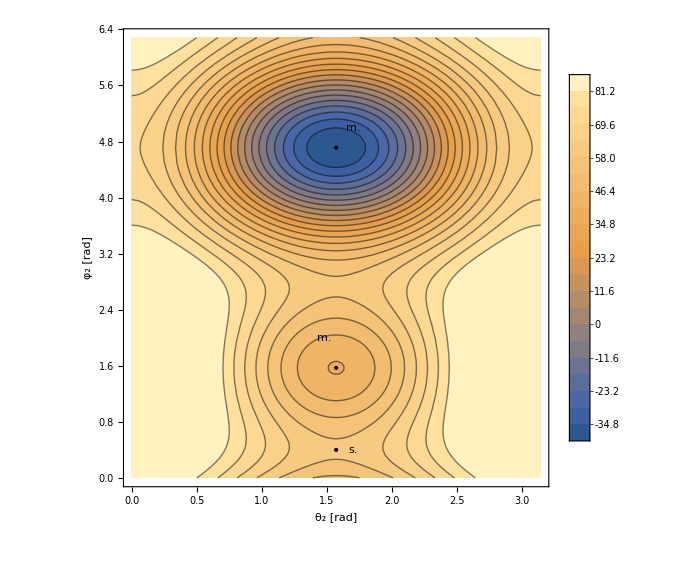

```mathematica
Show[{energyfunction2X[SPIN],point1x2,point2x2,point3x2},Epilog->{Inset[Text[Style["m.",20,Bold,FontFamily->"Times New Roman",Red],Background->None],{1.48,2}],Inset[Text[Style["m.",20,Bold,FontFamily->"Times New Roman",Red],Background->None],{1.7,5}],Inset[Text[Style["s.",20,Bold,FontFamily->"Times New Roman",Blue],Background->None],{1.7,0.4}]},ImageSize->Large]
```

# 3 - axis quantization (MOI-3 is the largest)

## Constants

0.971482 2.43662

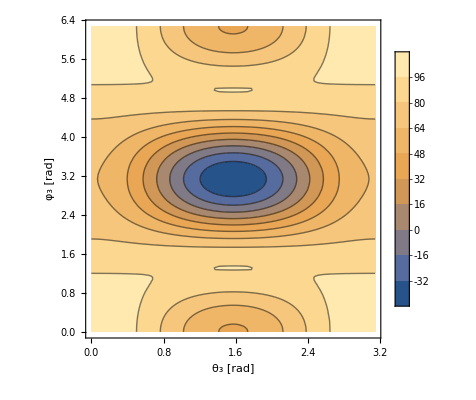

```mathematica
SPIN=19/2;
j=N[11/2];
THETA=N[70*π/180];
I1=10;I2=20;I3=40;
A1=1/(2I1);A2=1/(2I2);A3=1/(2I3);
u[spin_]:=N[ufct[spin,j,A1,A2,A3,THETA]];
v0[spin_]:=N[v0fct[spin,j,A1,A2,THETA]];
k[spin_]:=N[√ufct[spin,j,A1,A2,A3,THETA]];
Print[u[SPIN]," " ,v0[SPIN]]
HSph3x[I_,θ_,φ_]:=I^2 Cos[θ]^2(u[I]-Sin[φ]^2-v0[I]/I Cos[φ])+I^2 Sin[φ]^2+2v0[I]I*Cos[φ];
energyfunction3X[spin_]:=ContourPlot[HSph3x[spin,theta,fi],{theta,0,π},{fi,0,2π}(*PlotLabel->StringTemplate["H'(θ_1,φ_1); I=``"][SPIN]*),FrameLabel->{"θ_3 [rad]","φ_3 [rad]"},Contours->11,PlotLegends->Automatic,PlotRange->{-50,150},LabelStyle->{17,Bold,Black,FontFamily->"Times New Roman"},ClippingStyle->Automatic];
Show[{energyfunction3X[SPIN]}]
```

### Extremal points

```mathematica
P1x3[I_]:={π/2,π};(*minimum A1*)
P1x3Plus[I_]:={π/2,2π};(*minimum A1*)
P2x3[I_]:={π/2,0};(*minimum A2*)
P3x3[I_]:={π/2,ArcCos[v0[I]/I]};(*Maximum A3*)
P3x3Plus[I_]:={π/2,ArcCos[v0[I]/I]+1.16π};(*Maximum A3*)
point1x3=Graphics[Style[Point[P1x3[SPIN]],Red,PointSize[0.02]]];
point1x3Plus=Graphics[Style[Point[P1x3Plus[SPIN]],Red,PointSize[0.02]]];
point2x3=Graphics[Style[Point[P2x3[SPIN]],Red,PointSize[0.02]]];
point3x3=Graphics[Style[Point[P3x3[SPIN]],Blue,PointSize[0.02]]];
point3x3Plus=Graphics[Style[Point[P3x3Plus[SPIN]],Blue,PointSize[0.02]]];
Print[HSph3x[SPIN,P1x3[SPIN][[1]],P1x3[SPIN][[2]]]," ",HSph3x[SPIN,P2x3[SPIN][[1]],P2x3[SPIN][[2]]]," ",HSph3x[SPIN,P3x3[SPIN][[1]],P3x3[SPIN][[2]]]]
```

-46.2958 46.2958 96.1871

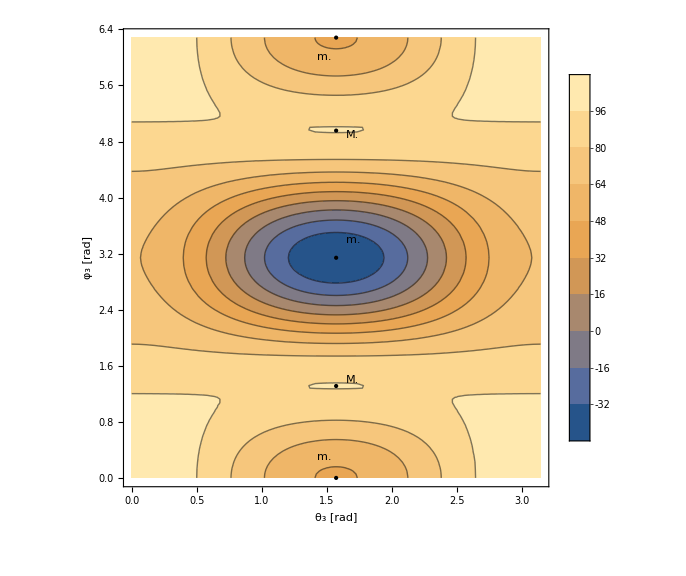

```mathematica
Show[{energyfunction3X[SPIN],point1x3,point2x3,point3x3,point3x3Plus,point1x3Plus},Epilog->{Inset[Text[Style["m.",20,Bold,FontFamily->"Times New Roman",Red],Background->None],{1.48,0.3}],Inset[Text[Style["m.",20,Bold,FontFamily->"Times New Roman",Red],Background->None],{1.48,6}],Inset[Text[Style["m.",20,Bold,FontFamily->"Times New Roman",Red],Background->None],{1.7,3.4}],Inset[Text[Style["M.",20,Bold,FontFamily->"Times New Roman",Blue],Background->None],{1.7,1.4}],Inset[Text[Style["M.",20,Bold,FontFamily->"Times New Roman",Blue],Background->None],{1.7,4.9}]},ImageSize->Large]
```